### Process Stream of images

Open an image from file eventually, grab frame from video
Blur image
Binarize it
Search for umbrellas
label umbrellas
Determine color of umbrellas -- quantize this?  Histogram this?

[compare the # detected with a downsampled image.  This worked well]

example/TrackingObjectsInAnImageSequence

```mathematica
fig =Import[StringJoin[NotebookDirectory[],"KeyFrames/frameRel0000003.jpg"]]
(*mfig =MeanFilter[fig,15]*)
```

-Graphics-

```mathematica
b1=Binarize[Blur[fig,3]]
(*b1=Binarize[mfig]*)  (*mean blur was bad*)
b=DeleteSmallComponents[b1,500];
distT=DistanceTransform[b,Padding-> 0];
marker = MaxDetect[ImageAdjust[distT],0.02];
w = WatershedComponents[GradientFilter[b,3],marker, Method-> "Rainfall"];
Colorize[w]
```

-Graphics-

```mathematica
umbrellas = SelectComponents[w,"Count",500<#<6000 &];
measures = ComponentMeasurements[umbrellas, {"Centroid","EquivalentDiskRadius","Label"}];
Show[fig,Graphics[{White, Circle@@ # &/@(measures⟦All,2,1
;;2⟧),MapThread[Text,{measures⟦All,2,3⟧,measures⟦All,2,1⟧}]}],ImageSize->Large]
Max[measures⟦All,2,3⟧]
```

-Graphics-

112

```mathematica
Max[measures⟦All,2,3⟧]
```

164

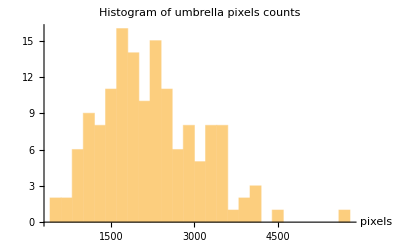

```mathematica
Histogram[ComponentMeasurements[umbrellas,"Count"]⟦All,2⟧,20,AxesLabel-> {"pixels"},PlotLabel-> "Histogram of umbrella pixels counts"]
```

```mathematica
smFig = ImageResize[fig,300];
DominantColors[smFig]
```

{-Graphics-}

```mathematica
noBack = ColorReplace[smFig,Black,0.05]
```

-Graphics-

```mathematica
DominantColors[RemoveAlphaChannel[noBack,White],10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DominantColors[fig]
```

$Aborted

```mathematica
res=DominantColors[fig,Automatic,{"CoverageImage","Color"}]
```

```mathematica
f2=Sharpen[Blur[fig,10],15]
b4=Binarize[Blur[f2,3]];
b5=DeleteSmallComponents[b4,500];
(*processing the blurred/sharpened image didn't improve result*)
```

```mathematica
b5
```

```mathematica
fig =Import[StringJoin[NotebookDirectory[],"KeyFrames/frameRel0000003.jpg"]];

smFig = ImageResize[fig,300];
b=Binarize[smFig];
distT=DistanceTransform[b,Padding-> 0];
marker = MaxDetect[ImageAdjust[distT],0.02];
w = WatershedComponents[GradientFilter[b,2],marker, Method-> "Rainfall"];
Colorize[w]

umbrellas = SelectComponents[w,"Count",10<#<150 &];
measures = ComponentMeasurements[umbrellas, {"Centroid","EquivalentDiskRadius","Label"}];
Show[smFig,Graphics[{White, Circle@@ # &/@(measures⟦All,2,1
;;2⟧),MapThread[Text,{measures⟦All,2,3⟧,measures⟦All,2,1⟧}]}],ImageSize->Large]
Max[measures⟦All,2,3⟧]
```

-Graphics-

-Graphics-

138

### How do I get the dominant color at a given location?

```mathematica
iDim = ImageDimensions[smFig];
sam = 200;
oneUmbrella=ImageTake[smFig,
Clip[Round[iDim⟦2⟧-measures⟦sam,2,1,2⟧+measures⟦sam,2,2⟧*.7*{-1,1}],{1,iDim⟦2⟧} ],
Clip[Round[measures⟦sam,2,1,1⟧+measures⟦sam,2,2⟧*.7*{-1,1}],{1,iDim⟦1⟧} ]]
colorsInImage =DominantColors[oneUmbrella,1]
```

Part::partw: Part 200 of {1 → {{1094.64, 1063.98}, 24.391, 1}, 2 → {{814.643, 1057.38}, 32.7619, 2}, 3 → {{947.1, 1052.82}, 34.8749, 3}, « 46 », 58 → {{156.924, 732.375}, 20.5135, 58}, « 50 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ImageTake::taker: Cannot take the specified rows of the image.

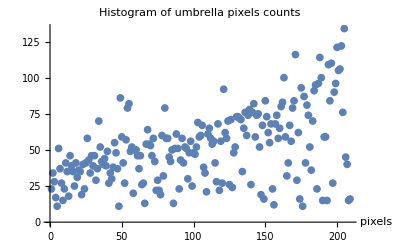

```mathematica
ListPlot[ComponentMeasurements[umbrellas,"Count"]⟦All,2⟧,AxesLabel-> {"pixels"},PlotLabel-> "Histogram of umbrella pixels counts"]
```

```mathematica
NotebookDirectory[]<>"KeyFrames/frameRel"<>IntegerString[5,7,4]<>".jpg"
```

/Users/ab55/Desktop/git/visionTracking/KeyFrames/frameRel0005.jpg

/Users/ab55/Desktop/git/visionTracking/KeyFrames/frameRel0000002.jpg

-Graphics-

### ProcessMany Images

```mathematica
frameData = Table[
filename = NotebookDirectory[]<>"KeyFrames/frameRel"<>IntegerString[i,10,7]<>".jpg";
fig =Import[filename];

smFig = ImageResize[fig,300];
b=Binarize[smFig];
distT=DistanceTransform[b,Padding-> 0];
marker = MaxDetect[ImageAdjust[distT],0.02];
w = WatershedComponents[GradientFilter[b,2],marker, Method-> "Rainfall"];
Colorize[w];
umbrellas = SelectComponents[w,"Count",8<#<150 &];
measures = ComponentMeasurements[umbrellas, {"Centroid","EquivalentDiskRadius","Label"}];
{Show[smFig,Graphics[{White, Circle@@ # &/@(measures⟦All,2,1
;;2⟧),MapThread[Text,{measures⟦All,2,3⟧,measures⟦All,2,1⟧}]}],ImageSize->Large],
Max[measures⟦All,2,3⟧]},
{i,1,9}]
```

{{-Graphics-,214},{-Graphics-,188},{-Graphics-,138},{-Graphics-,167},{-Graphics-,186},{-Graphics-,182},{-Graphics-,138},{-Graphics-,115},{-Graphics-,162}}

```mathematica
N[(200-15)/200]
```

0.925

```mathematica
N[Mean[frameData[[All,2]]]]
```

165.778

```mathematica
ImageCollage[frameData[[All,1]],Automatic,10000,ImagePadding->2,Background->White]
```

```mathematica
Grid[Transpose[{frameData[[All,1]]}]]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"Processed1.pdf",frameData[[1,1]]]
```

/Users/ab55/Desktop/git/visionTracking/Processed1.pdf